# 4. Regula Falsi Method

```mathematica
regulafalsi[f_,a0_,b0_,n_]:=Module[{},a=N[a0];
b=N[b0];c=(a*f[b]-b*f[a])/(f[b]-f[a]);k=0;
Print["________________________________________"];
Print["S.No.", "            ","C","              ","F[C]"];
Print["________________________________________"];
While[k<n,If[f[a]*f[c]<0,b=c,a=c;
Print[k,"      ",NumberForm[c,10],"      ",NumberForm[f[c],10]];];
c=(a*f[b]-b*f[a])/(f[b]-f[a]);
k=k+1;];
Print[" "];
Print["c = ",NumberForm[c,16]];Print["f[c]",NumberForm[f[c],16]];
Plot[f[x],{x,-3,3},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed],PlotStyle->{Thickness[0.004],Magenta},PlotLegends->{f[x]},Frame->True]]
```

## Question - 1

________________________________________

S.No.            C              F[C]

________________________________________

0      1.571428571      -1.364431487

1      1.705410822      -0.2477450996

2      1.727882728      -0.03933955131

3      1.731404866      -0.006110673094

4      1.731950853      -0.000945920667

c = 1.732035343851165

f[c]-0.0001463487141180053

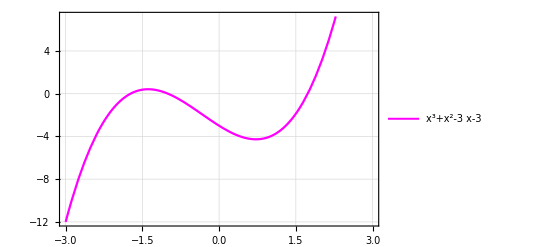

```mathematica
f[x_] := x^3+x^2-3*x-3
regulafalsi[f,1,2,5]
```

## Question - 2

1-3 x+x^2

________________________________________

S.No.            C              F[C]

________________________________________

0      2.      -1.

1      2.5      -0.25

2      2.6      -0.04

3      2.615384615      -0.005917159763

4      2.617647059      -0.0008650519031

5      2.617977528      -0.000126246686

6      2.618025751      -0.00001841993774

7      2.618032787      -2.68744961×10^-6

8      2.618033813      -3.920939751×10^-7

9      2.618033963      -5.720574681×10^-8

c = 2.618033985017358

f[c]-8.34620639267314×10^-9

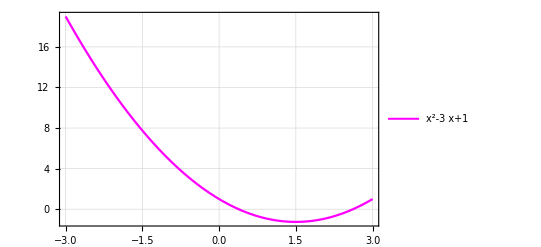

```mathematica
f[x_] = x^2-3*x+1
regulafalsi[f,1,3,10]
```

## Question - 3

x^4+Cos[x]

________________________________________

S.No.            C              F[C]

________________________________________

0      -1.850815718      11.45780491

1      1.442764494      4.460613441

2      0.7664662634      1.065487768

3      0.2424146185      0.9742144899

4      -1.061359522      1.756651926

c = 15.67586039879742

f[c]60383.51084576982

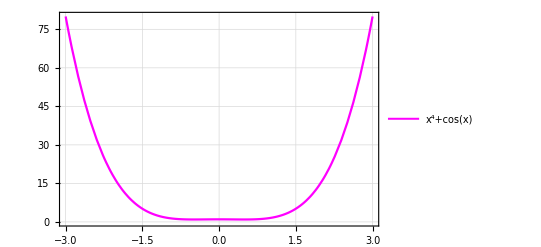

```mathematica
f[x_] = Cos[x]+x^4
regulafalsi[f,0,1,5]
```

## Question -4

x^3

________________________________________

S.No.            C              F[C]

________________________________________

0      0.9230769231      0.7865270824

1      0.8607594937      0.6377426532

2      0.8090080485      0.5294909319

3      0.7651815256      0.4480159007

4      0.7274730739      0.384991171

c = 0.6946005391326552

f[c]0.3351238588812435

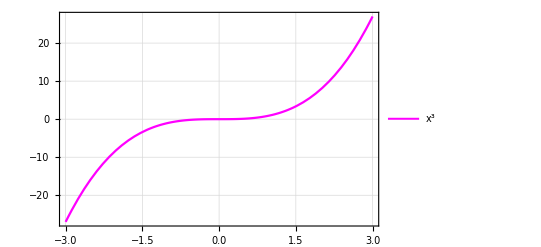

```mathematica
f[x_] = x^3
regulafalsi[f,1,3,5]
```